# Wolfram Summer School HW Week 1: Fourier Series

The Fourier Series is a representation of a function as an infinite sum of sinusoids.

## The Fourier Series

### History

Jean-Baptiste Joseph Fourier introduced the Fourier Series as a way of solving the heat equation in a metal plate. In turn, he concluded that any arbitrary continuous function can be represented by a trigonometric series based on the set of Sin(n·x) and Cos(n·x) functions. In general, the techniques are quite useful when applied to differential equations involving eigen-solutions that are sinusoids.

### Motivation

Consider a function that does not have a closed form integral formula (i.e. cannot be expressed without using numeric methods):

Plot said function: Sin(x^2)

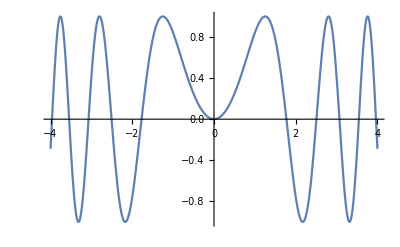

```mathematica
Plot[Sin[x^2],{x,-4,4}]
```

We attempt to the take the integral...

Integrate the function:

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

and we can plot the function numerically -

Plot the integral formula:

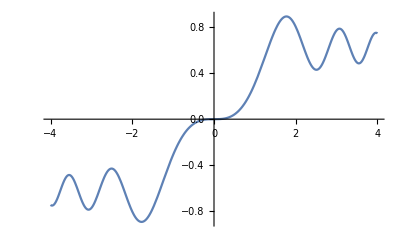

```mathematica
Plot[%,{x,-4,4}]
```

However there does not exist a closed form solution to such an integral equation.

### Theory

We can define a series of sinusoids that converge to the original function, with the correct constants.

Find the first coefficient in the Fourier Series:

```mathematica
FourierCoefficient[Sin[x^2],x,1]
```

-1/(8 √π)(-1)^(1/4) ⅇ^(-ⅈ/4) (ⅇ^(ⅈ/2) (Erf[1/2 (-1)^(1/4) (1-2 π)]-Erf[1/2 (-1)^(1/4) (1+2 π)])-Erfi[1/2 (-1)^(1/4) (-1-2 π)]+Erfi[1/2 (-1)^(1/4) (-1+2 π)])

Express it numerically:

```mathematica
N[%]
```

0.096227-1.38778×10^-17 ⅈ

Create a list of the first 3 coefficients in the series:

```mathematica
Table[FourierCoefficient[Sin[x^2],x,i],{i,1,3}]
```

{-1/(8 √π)(-1)^(1/4) ⅇ^(-ⅈ/4) (ⅇ^(ⅈ/2) (Erf[1/2 (-1)^(1/4) (1-2 π)]-Erf[1/2 (-1)^(1/4) (1+2 π)])-Erfi[1/2 (-1)^(1/4) (-1-2 π)]+Erfi[1/2 (-1)^(1/4) (-1+2 π)]),-1/(8 √π)(-1)^(1/4) ⅇ^-ⅈ (ⅇ^(2 ⅈ) (Erf[(-1)^(1/4) (1-π)]-Erf[(-1)^(1/4) (1+π)])+Erfi[(-1)^(1/4) (-1+π)]+Erfi[(-1)^(1/4) (1+π)]),-1/(8 √π)(-1)^(1/4) ⅇ^(-(9 ⅈ)/4) (ⅇ^((9 ⅈ)/2) (Erf[1/2 (-1)^(1/4) (3-2 π)]-Erf[1/2 (-1)^(1/4) (3+2 π)])-Erfi[1/2 (-1)^(1/4) (-3-2 π)]+Erfi[1/2 (-1)^(1/4) (-3+2 π)])}

```mathematica
N[%]
```

{0.096227-1.38778×10^-17 ⅈ,-0.00837573+6.48353×10^-17 ⅈ,-0.340173+2.77556×10^-17 ⅈ}

We attach these constants to the corresponding functions and obtain an approximation.

Create the 1st order Fourier Series of the function:

```mathematica
FourierSeries[Sin[x^2],x,1]
```

-1/(8 √π)(-1)^(1/4) ⅇ^(-ⅈ/4+ⅈ x) (ⅇ^(ⅈ/2) (Erf[1/2 (-1)^(1/4) (1-2 π)]-Erf[1/2 (-1)^(1/4) (1+2 π)])-Erfi[1/2 (-1)^(1/4) (-1-2 π)]+Erfi[1/2 (-1)^(1/4) (-1+2 π)])-1/(8 √π)(-1)^(1/4) ⅇ^(-ⅈ/4-ⅈ x) (ⅇ^(ⅈ/2) (Erf[1/2 (-1)^(1/4) (1-2 π)]-Erf[1/2 (-1)^(1/4) (1+2 π)])-Erfi[1/2 (-1)^(1/4) (1-2 π)]+Erfi[1/2 (-1)^(1/4) (1+2 π)])+FresnelS[√(2 π)]/(√(2 π))

Create the 3rd order Fourier Series of the function:

```mathematica
fourierSeries3=FourierSeries[Sin[x^2],x,3]//N
```

0.245943+(0.0932356+0.0238069 ⅈ) 2.71828^((0.-0.25 ⅈ)-(0.+1. ⅈ) x)+(0.0932356+0.0238069 ⅈ) 2.71828^((0.-0.25 ⅈ)+(0.+1. ⅈ) x)-(0.00452542+0.00704793 ⅈ) 2.71828^((0.-1. ⅈ)-(0.+2. ⅈ) x)-(0.00452542+0.00704793 ⅈ) 2.71828^((0.-1. ⅈ)+(0.+2. ⅈ) x)+(0.213688-0.264679 ⅈ) 2.71828^((0.-2.25 ⅈ)-(0.+3. ⅈ) x)+(0.213688-0.264679 ⅈ) 2.71828^((0.-2.25 ⅈ)+(0.+3. ⅈ) x)

and we can plot said function with Sin(x^2) to compare.

Plot Sin(x^2) and our Fourier Series approximation on the same graph:

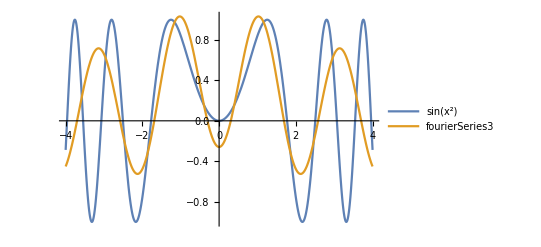

```mathematica
Plot[{Sin[x^2],fourierSeries3},{x,-4,4},PlotLegends->"Expressions"]
```

### Mathematical Exploration

While we can see that the functions do not overlap exactly, we will explore the convergence of the series.

Create the 1st order Fourier Series approximation:

```mathematica
fourierSeries1=N[FourierSeries[Sin[x^2],x,1]];
```

and plot:

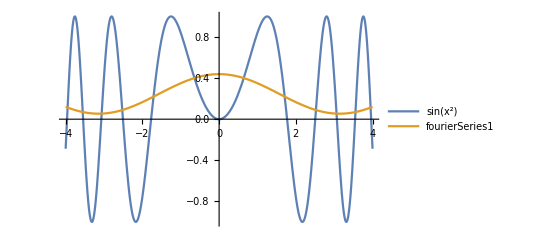

```mathematica
Plot[{Sin[x^2],fourierSeries1},{x,-4,4},PlotLegends->"Expressions"]
```

Create the 4th order Fourier Series approximation:

```mathematica
fourierSeries4=N[FourierSeries[Sin[x^2],x,4]];
```

and plot:

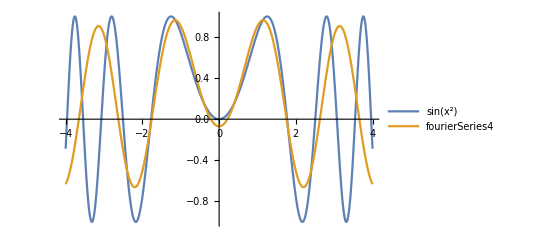

```mathematica
Plot[{Sin[x^2],fourierSeries4},{x,-4,4},PlotLegends->"Expressions"]
```

Create the 7th order Fourier Series approximation:

```mathematica
fourierSeries7=N[FourierSeries[Sin[x^2],x,7]];
```

and plot:

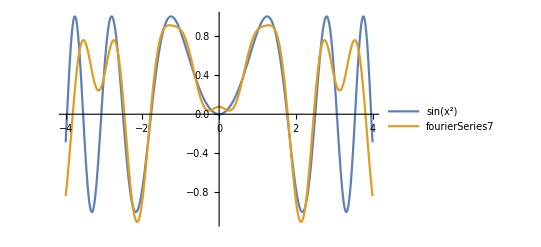

```mathematica
Plot[{Sin[x^2],fourierSeries7},{x,-4,4},PlotLegends->"Expressions"]
```

### Application: Numerical Analysis

We can then compare the numerical integral to the integral of the Fourier Series (of which all the terms are integrable).

Compute a list of differences between the integrals as the order of the series increases and plot:

```mathematica
Table[NIntegrate[Sin[x^2],{x,-2,2}]-NIntegrate[FourierSeries[Sin[x^2],x,i],{x,-2,2}],{i,1,6}]
```

{0.275786,0.263109,0.136376,0.0427577,0.0894727,0.0431002}

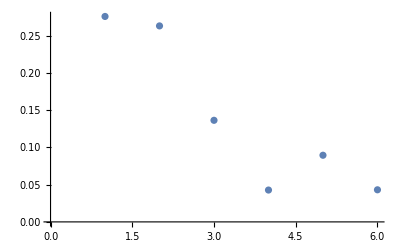

```mathematica
ListPlot[%]
```

and we can see that the difference is tending towards 0. Thus taking the integral of the Fourier Series of a function is one way to approximate the area under a curve.

### Another Application: Solving Differential Equations

Consider the differential equation: y’’  = - kx, k > 0 with boundary condition y(0) = 0, y’(0) = 0. 
We will solve this using Fourier series.

First find the Fourier Series of the right-hand side of the equation.
We show the first few terms here:

```mathematica
ComplexExpand[FourierSeries[-k*x,x,8]]
```

-2 k Sin[x]+k Sin[2 x]-2/3 k Sin[3 x]+1/2 k Sin[4 x]-2/5 k Sin[5 x]+1/3 k Sin[6 x]-2/7 k Sin[7 x]+1/4 k Sin[8 x]

We now assume that y(x) can be written similarly [ y(x) = ∑_(n=1)^∞ b_n*Sin(n*x) ] and substitute.

To begin, we compute the second derivative on the left-hand side of the equation for each term:

```mathematica
lhs=D[D[b*Sin[n*x],x],x]
```

-b n^2 Sin[n x]

Since each term in the sum on the left-hand side and right-hand side must be equal, an equation involving solely b_n follows.

We then solve for the unknown coefficients, after generalizing the coefficients on the right-hand side. 
For the even terms:

```mathematica
Solve[-b*n^2==k/n,b]
```

{{b→-k/n^3}}

For the odd terms:

```mathematica
Solve[-b*n^2==-2*k/(2n+1),b]
```

{{b→(2 k)/(n^2 (1+2 n))}}

Thus our solution becomes y(x) = ∑_(n=1)^∞ (2 k)/(n^2 (1+2 n))*Sin[n*x] + ∑_(n=1)^∞ -k/n^3*Sin[n*x].

Sum up the terms, set k = 1, and plot the solution:

```mathematica
sol[x_]=Sum[(2 k)/(n^2 (1+2 n))*Sin[n*x]+-k/n^3*Sin[n*x],{n,1,Infinity}]/.k->1;
```

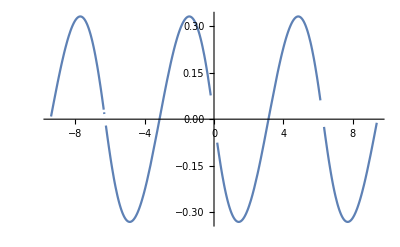

```mathematica
Plot[sol[x],{x,-3*Pi,3*Pi}]
```

Further Explorations

Explore the Taylor Series Expansion of a Function

Explore Other Sets of Basis Functions That Can Approximate a Function

Authorship information

Michael Dobbs

21.06.17

dobbsm@sonoma.edu